```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:={{{(x1+2 x2)/3,(y1+2 y2)/3},{(2 x1+x2)/3,(2 y1+y2)/3},{(x1+x2+x3)/3,(y1+y2+y3)/3}},{{(x1+2 x2)/3,(y1+2 y2)/3},{(2 x2+x3)/3,(2 y2+y3)/3},{(x1+x2+x3)/3,(y1+y2+y3)/3}},{{(x2+2 x3)/3,(y2+2 y3)/3},{(2 x2+x3)/3,(2 y2+y3)/3},{(x1+x2+x3)/3,(y1+y2+y3)/3}},{{(x2+2 x3)/3,(y2+2 y3)/3},{(2 x3+x1)/3,(2 y3+y1)/3},{(x1+x2+x3)/3,(y1+y2+y3)/3}},{{(x3+2 x1)/3,(y3+2 y1)/3},{(2 x3+x1)/3,(2 y3+y1)/3},{(x1+x2+x3)/3,(y1+y2+y3)/3}},{{(x3+2 x1)/3,(y3+2 y1)/3},{(2 x1+x2)/3,(2 y1+y2)/3},{(x1+x2+x3)/3,(y1+y2+y3)/3}}};

a2[a_]:=Join@@(a1/@a);

list=Nest[a2,{{{0.,0.},{1./2,Sqrt[3.]/2},{1.,0.}}},6];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

-Graphics-

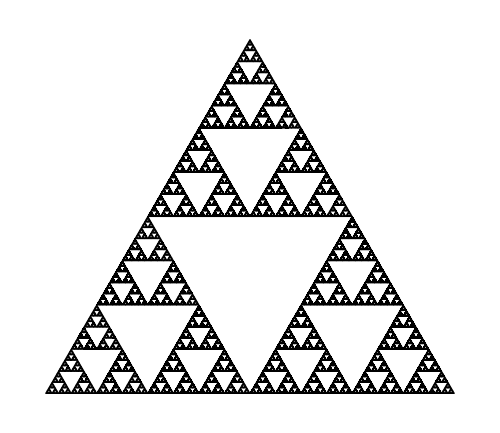

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:={{{x1,y1},{(x1+x2)/2,(y1+y2)/2},{(x1+x3)/2,(y1+y3)/2}},{{x2,y2},{(x2+x3)/2,(y2+y3)/2},{(x2+x1)/2,(y2+y1)/2}},{{x3,y3},{(x3+x1)/2,(y3+y1)/2},{(x3+x2)/2,(y3+y2)/2}}};

a2[a_]:=Join@@(a1/@a);

list=Nest[a2,{{{0.,0.},{1./2,Sqrt[3.]/2},{1.,0.}}},7];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}}]:={{{x1,y1},{(2 x1+x2)/3,(2 y1+y2)/3},{(2 x1+x3)/3,(2 y1+y3)/3},{(2 x1+x4)/3,(2 y1+y4)/3}},{{x2,y2},{(2 x2+x3)/3,(2 y2+y3)/3},{(2 x2+x4)/3,(2 y2+y4)/3},{(2 x2+x1)/3,(2 y2+y1)/3}},{{x3,y3},{(2 x3+x4)/3,(2 y3+y4)/3},{(2 x3+x1)/3,(2 y3+y1)/3},{(2 x3+x2)/3,(2 y3+y2)/3}},{{x4,y4},{(2 x4+x1)/3,(2 y4+y1)/3},{(2 x4+x2)/3,(2 y4+y2)/3},{(2 x4+x3)/3,(2 y4+y3)/3}},{{(2 x1+x2)/3,(2 y1+y2)/3},{(2 x2+x1)/3,(2 y2+y1)/3},{(2 x2+x4)/3,(2 y2+y4)/3},{(2 x1+x3)/3,(2 y1+y3)/3}},{{(2 x2+x3)/3,(2 y2+y3)/3},{(2 x3+x2)/3,(2 y3+y2)/3},{(2 x3+x1)/3,(2 y3+y1)/3},{(2 x2+x4)/3,(2 y2+y4)/3}},{{(2 x3+x4)/3,(2 y3+y4)/3},{(2 x4+x3)/3,(2 y4+y3)/3},{(2 x4+x2)/3,(2 y4+y2)/3},{(2 x3+x1)/3,(2 y3+y1)/3}},{{(2 x4+x1)/3,(2 y4+y1)/3},{(2 x1+x4)/3,(2 y1+y4)/3},{(2 x1+x3)/3,(2 y1+y3)/3},{(2 x4+x2)/3,(2 y4+y2)/3}}};

a2[a_]:=Join@@(a1/@a);

list=Nest[a2,{{{0.,0.},{1.,0.},{1.,1.},{0.,1.}}},5];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

-Graphics-

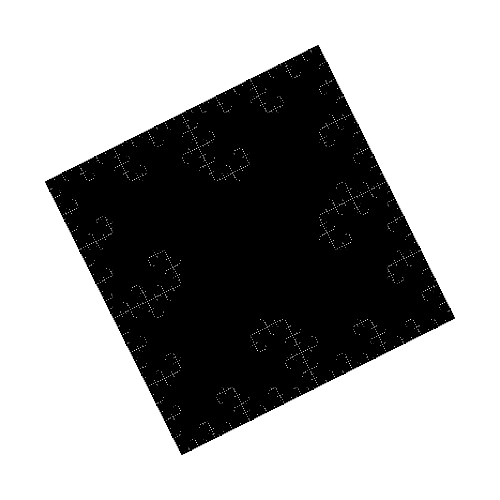

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}}]:={{{x1,y1},{x1+(y2-y1)/2,y1-(x2-x1)/2},{x1+(y3-y1)/2,y1-(x3-x1)/2},{x1+(y4-y1)/2,y1-(x4-x1)/2}},{{x2,y2},{x2+(y3-y2)/2,y2-(x3-x2)/2},{x2+(y4-y2)/2,y2-(x4-x2)/2},{x2+(y1-y2)/2,y2-(x1-x2)/2}},{{x3,y3},{x3+(y4-y3)/2,y3-(x4-x3)/2},{x3+(y1-y3)/2,y3-(x1-x3)/2},{x3+(y2-y3)/2,y3-(x2-x3)/2}},{{x4,y4},{x4+(y1-y4)/2,y4-(x1-x4)/2},{x4+(y2-y4)/2,y4-(x2-x4)/2},{x4+(y3-y4)/2,y4-(x3-x4)/2}}};

a2[a_]:=Join@@(a1/@a);

list=Join@@NestList[a2,{{{0.,0.},{1.,0.},{1.,1.},{0.,1.}}},7];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

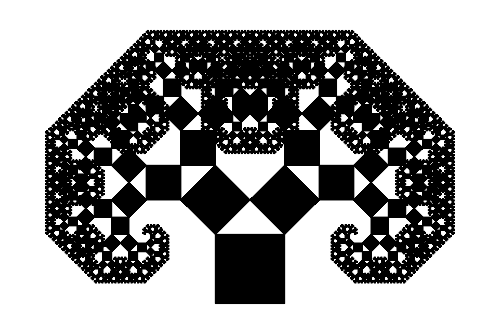

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}}]:={{{x3+(x1-x2)/2+(y1-y2)/2,y3+(y1-y2)/2-(x1-x2)/2},{x3,y3},{x3+(x3-x2)/2+(y3-y2)/2,y3+(y3-y2)/2-(x3-x2)/2},{x3+(x4-x2)/2+(y4-y2)/2,y3+(y4-y2)/2-(x4-x2)/2}},{{x4,y4},{x4+(x2-x1)/2-(y2-y1)/2,y4+(y2-y1)/2+(x2-x1)/2},{x4+(x3-x1)/2-(y3-y1)/2,y4+(y3-y1)/2+(x3-x1)/2},{x4+(x4-x1)/2-(y4-y1)/2,y4+(y4-y1)/2+(x4-x1)/2}}};

a2[a_]:=Join@@(a1/@a);

list=Join@@NestList[a2,{{{0.,0.},{1.,0.},{1.,1.},{0.,1.}}},12];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

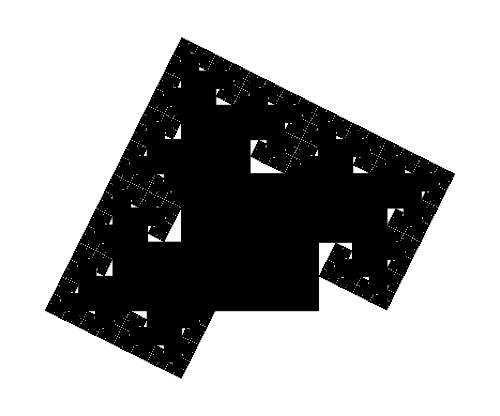

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}}]:={{{x3,y3},{x3-(y4-y3)/2,y3+(x4-x3)/2},{x3-(y1-y3)/2,y3+(x1-x3)/2},{x3-(y2-y3)/2,y3+(x2-x3)/2}},{{x4,y4},{x4-(y1-y4)/2,y4+(x1-x4)/2},{x4-(y2-y4)/2,y4+(x2-x4)/2},{x4-(y3-y4)/2,y4+(x3-x4)/2}},{{x1,y1},{x1-(y2-y1)/2,y1+(x2-x1)/2},{x1-(y3-y1)/2,y1+(x3-x1)/2},{x1-(y4-y1)/2,y1+(x4-x1)/2}}};

a2[a_]:=Join@@(a1/@a);

list=Join@@NestList[a2,{{{0.,0.},{1.,0.},{1.,1.},{0.,1.}}},7];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

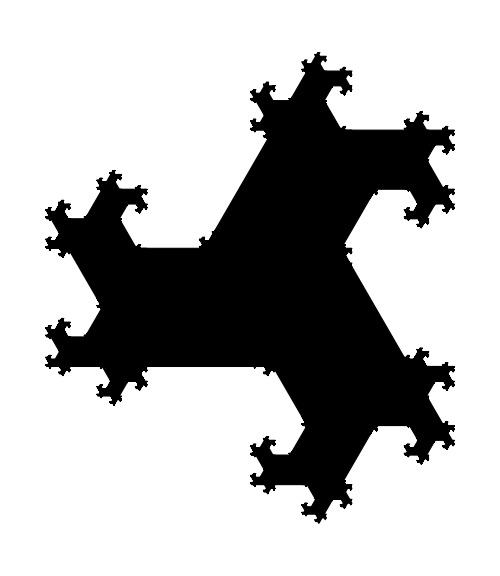

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:={{{x1,y1},{x1+(x2-x1)/4-Sqrt[3] (y2-y1)/4,y1+Sqrt[3] (x2-x1)/4+(y2-y1)/4},{x1+(x3-x1)/4-Sqrt[3] (y3-y1)/4,y1+Sqrt[3] (x3-x1)/4+(y3-y1)/4}},{{x2,y2},{x2+(x3-x2)/4-Sqrt[3] (y3-y2)/4,y2+Sqrt[3] (x3-x2)/4+(y3-y2)/4},{x2+(x1-x2)/4-Sqrt[3] (y1-y2)/4,y2+Sqrt[3] (x1-x2)/4+(y1-y2)/4}},{{x3,y3},{x3+(x1-x3)/4-Sqrt[3] (y1-y3)/4,y3+Sqrt[3] (x1-x3)/4+(y1-y3)/4},{x3+(x2-x3)/4-Sqrt[3] (y2-y3)/4,y3+Sqrt[3] (x2-x3)/4+(y2-y3)/4}}};

a2[a_]:=Join@@(a1/@a);

list=Join@@NestList[a2,{{{0.,0.},{1./2,Sqrt[3.]/2},{1.,0.}}},7];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```

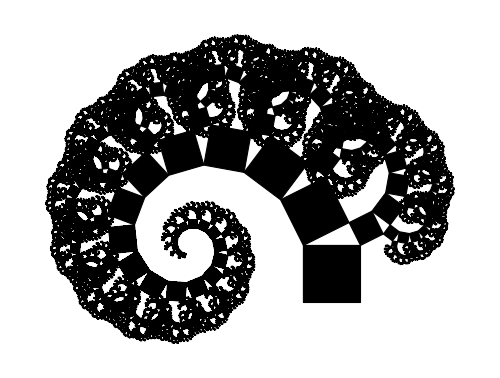

```mathematica
a1[{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}}]:=If[(x2-x1)^2+(y2-y1)^2<0.0002,{},{{{x3+(x1-x2)/5+2 (y1-y2)/5,y3+(y1-y2)/5-2 (x1-x2)/5},{x3,y3},{x3+(x3-x2)/5+2 (y3-y2)/5,y3+(y3-y2)/5-2 (x3-x2)/5},{x3+(x4-x2)/5+2 (y4-y2)/5,y3+(y4-y2)/5-2 (x4-x2)/5}},{{x4,y4},{x4+4 (x2-x1)/5-2 (y2-y1)/5,y4+4 (y2-y1)/5+2 (x2-x1)/5},{x4+4 (x3-x1)/5-2 (y3-y1)/5,y4+4 (y3-y1)/5+2 (x3-x1)/5},{x4+4 (x4-x1)/5-2 (y4-y1)/5,y4+4 (y4-y1)/5+2 (x4-x1)/5}}}];

a2[a_]:=Join@@(a1/@a);

list=Join@@NestList[a2,{{{0.,0.},{1.,0.},{1.,1.},{0.,1.}}},23];

Graphics[{EdgeForm[Thickness[Tiny]],Polygon[#]&/@list},ImageSize->500]
```